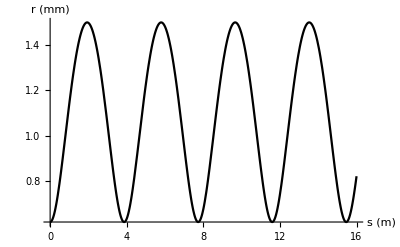

```mathematica
Clear["`*"];jingdu=50;
fx[huatu_,r0_?NumberQ,r0dao_?NumberQ,bianjie_:1]:=Block[{η,r},
{η=1/2};
Module[{zhong,rhh,jieguo,tu},r00=r/.NDSolve[{r''[s]+r[s]-η^2/r[s]^3-(1-η^2)/r[s]==0,r[0]==r0,r'[0]==r0dao},{r},{s,0,bianjie},WorkingPrecision->jingdu,PrecisionGoal-> 15,AccuracyGoal->15,MaxSteps->Infinity][[1]];tu=Plot[r00[x],{x,0,bianjie},PlotRange->All,PlotStyle->{Bold,Black},AxesLabel->{Style["s (m)",Black],Style["r (mm)",Black]},LabelStyle->Directive[Bold],AxesStyle->Directive[Thick,Italic]];
If[huatu==1,tu,r00//N]]]
fx[1,62/100,0,16]
```

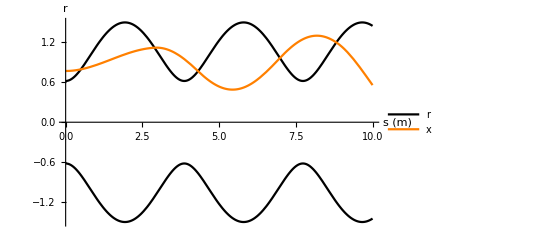

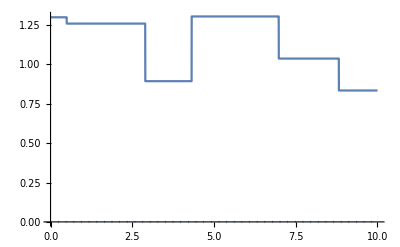

```mathematica
Clear["`*"];jingdu=50;fxyzyan[huatu_,r0_?NumberQ,r0dao_?NumberQ,xxiao0_?NumberQ,xxiao0dao_?NumberQ,bianjie_:10]:=Module[{η=1/2,r,x,zhong,rhh,jieguo,tu,can1,can2,can3,solx,dians},r=r/.NDSolve[{r''[s]+r[s]-η^2/r[s]^3-(1-η^2)/r[s]==0,r[0]==r0,r'[0]==r0dao},{r},{s,0,bianjie},WorkingPrecision->jingdu,PrecisionGoal->15,AccuracyGoal->15,MaxSteps->Infinity][[1]];{solx,dians}=NDSolve[{x''[s]+x[s]- can1[s]*(1-η^2)==0,x[0]==xxiao0,x'[0]==xxiao0dao,can1[0]==If[And@@{Abs[x[0]]<Abs[r[0]]},x[0]/r[0]^2/.{x[0]->xxiao0},1/x[0]/.{x[0]->xxiao0}],WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]<0},{can1[s]->x[s]/r[s]^2},"LocationMethod"->"Brent"],
WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]>=0},{can1[s]->1/x[s]},"LocationMethod"->"Brent"],
WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]<0},Sow[{s,r[s],x[s]}],"LocationMethod"->"Brent"]},{x,can1[s]},{s,0,bianjie},DiscreteVariables->{can1[s]},MaxSteps->∞,InterpolationOrder->4]//Reap;{rn0,xnewn0,can1new}={r,x,can1[s]}/.solx[[1]];]
bianjie=10;
fxyzyan[0,62/100,0,77/100,0,bianjie]
Plot[{rn0[s],xnewn0[s],-rn0[s]},{s,0,bianjie},PlotRange->All,PlotLegends->{"r","x"},PlotStyle->{Directive[Bold,Black],Directive[Bold,Orange],Directive[Bold,Black]},AxesLabel->{Style["s (m)",Black],Style["r",Black]},LabelStyle->Directive[Bold],AxesStyle->Directive[Thick,Italic]]
ReImPlot[{can1new},{s,0,bianjie},PlotRange->All]
```

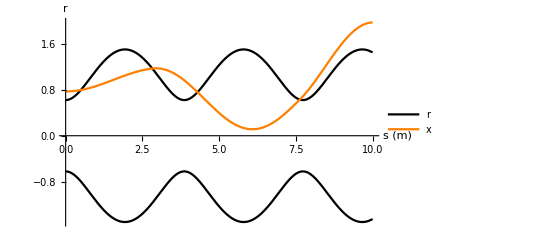

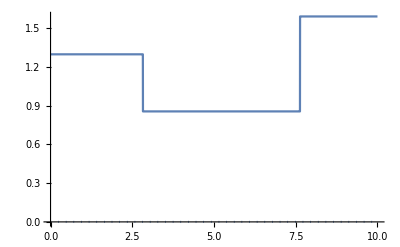

```mathematica
Clear["`*"];jingdu=50;fxyzyan[huatu_,r0_?NumberQ,r0dao_?NumberQ,xxiao0_?NumberQ,xxiao0dao_?NumberQ,bianjie_:10]:=Module[{η=1/2,r,x,zhong,rhh,jieguo,tu,can1,can2,can3,solx,dians},r=r/.NDSolve[{r''[s]+r[s]-η^2/r[s]^3-(1-η^2)/r[s]==0,r[0]==r0,r'[0]==r0dao},{r},{s,0,bianjie},WorkingPrecision->jingdu,PrecisionGoal->15,AccuracyGoal->15,MaxSteps->Infinity][[1]];{solx,dians}=NDSolve[{x''[s]+x[s]- can1[s]*(1-η^2)==0,x[0]==xxiao0,x'[0]==xxiao0dao,can1[0]==If[And@@{Abs[x[0]]<Abs[r[0]]},x[0]/r[0]^2/.{x[0]->xxiao0},1/x[0]/.{x[0]->xxiao0}],(*WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]<0},{can1[s]->x[s]/r[s]^2},"LocationMethod"->"Brent"],*)
WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]>=0},{can1[s]->1/x[s]},"LocationMethod"->"Brent"],
WhenEvent[And@@{Abs[Re@x[s]]-Abs[Re@r[s]]<0},Sow[{s,r[s],x[s]}],"LocationMethod"->"Brent"]},{x,can1[s]},{s,0,bianjie},DiscreteVariables->{can1[s]},MaxSteps->∞,InterpolationOrder->4]//Reap;{rn0,xnewn0,can1new}={r,x,can1[s]}/.solx[[1]];]
bianjie=10;
fxyzyan[0,62/100,0,77/100,0,bianjie]
Plot[{rn0[s],xnewn0[s],-rn0[s]},{s,0,bianjie},PlotRange->All,PlotLegends->{"r","x"},PlotStyle->{Directive[Bold,Black],Directive[Bold,Orange],Directive[Bold,Black]},AxesLabel->{Style["s (m)",Black],Style["r",Black]},LabelStyle->Directive[Bold],AxesStyle->Directive[Thick,Italic]]
ReImPlot[{can1new},{s,0,bianjie},PlotRange->All]
```